```mathematica
N-sf-N-I-S junction for YSR states
```

## N-sf-N-I-N junction for YSR states

## Spin up incident electron

```mathematica
Clear["Global`*"]


(*S= 0.5;
kfa= 0.5*π;
m1= -0.5;
Δ= 1;
Ef= 30;
J= 1.2;
F= 1;*)

u=1; v=0;
qp1=ke1; qm1=kh1;


a1=1;
a2=0;
a3=0;
a4=0;
a5=-1;
a6=0;
a7=-Exp[I*kfa*ke1];
a8=0;
a9=0;
a10=0;
a11=0;
a12=0;
a13=0;
a14=0;
a15=0;
a16=0;
z1=-1;


b1=0;
b2=1;
b3=0;
b4=0;
b5=0;
b6=-1;
b7=0;
b8=-Exp[I*kfa*ke1];
b9=0;
b10=0;
b11=0;
b12=0;
b13=0;
b14=0;
b15=0;
b16=0;
z2=0;


c1=0;
c2=0;
c3=1;
c4=0;
c5=0;
c6=0;
c7=0;
c8=0;
c9=-Exp[-I*kfa*kh1];
c10=0;
c11=-1; 
c12=0; 
c13=0;
c14=0;
c15=0;
c16=0;
z3=0;


d1=0;
d2=0;
d3=0;
d4=1;
d5=0;
d6=0;
d7=0;
d8=0;
d9=0;
d10=-Exp[-I*kfa*kh1]; 
d11=0;
d12=-1;
d13=0;
d14=0;
d15=0;
d16=0;
z4=0;


e1=ke1-I*J*m1;
e2=-I*J*F;
e3=0;
e4=0;
e5=ke1;
e6=0;
e7=-ke1*Exp[I*kfa*ke1];
e8=0;
e9=0;
e10=0;
e11=0;
e12=0;
e13=0;
e14=0;
e15=0;
e16=0;
z5=ke1+I*J*m1;


f1=-I*J*F;
f2=ke1+I*J*(m1+1);
f3=0;
f4=0;
f5=0;
f6=ke1;
f7=0;
f8=-ke1*Exp[I*kfa*ke1];
f9=0;
f10=0;
f11=0;
f12=0;
f13=0;
f14=0;
f15=0;
f16=0;
z6=I*J*F;


g1=0;
g2=0;
g3=-kh1+I*J*(m1+1); (* - I*)
g4=-I*J*F;
g5=0;
g6=0;
g7=0;
g8=0;
g9=kh1*Exp[-I*kfa*kh1];
g10=0;
g11=-kh1;
g12=0;
g13=0;
g14=0;
g15=0;
g16=0;
z7=0;


h1=0;
h2=0;
h3=-I*J*F;
h4=-kh1-I*J*(m1);
h5=0;
h6=0;
h7=0;
h8=0;
h9=0;
h10=kh1*Exp[-I*kfa*kh1];
h11=0;
h12=-kh1;
h13=0;
h14=0;
h15=0;
h16=0;
z8=0;


i1=0;
i2=0;
i3=0;
i4=0;
i5=Exp[I*kfa*ke1]; 
i6=0;  
i7=1;
i8=0;
i9=0;
i10=0;
i11=0;
i12=0;
i13=-u*Exp[I*kfa*qp1]; 
i14=0;
i15=0;
i16=-v*Exp[-I*kfa*qm1]; 
z9=0;


j1=0;
j2=0;
j3=0;
j4=0;
j5=0;
j6=Exp[I*kfa*ke1];
j7=0;
j8=1;
j9=0;      
j10=0;
j11=0;
j12=0;
j13=0;
j14=-u*Exp[I*kfa*qp1];  
j15=v*Exp[-I*kfa*qm1];    
j16=0;
z10=0;


t1=0;
t2=0;
t3=0;
t4=0;
t5=0;
t6=0;
t7=0;
t8=0;
t9=1;
t10=0;
t11=Exp[-I*kfa*kh1]; 
t12=0;
t13=0;
t14=v*Exp[I*kfa*qp1];
t15=-u*Exp[-I*kfa*qm1];  
t16=0;      
z11=0;


l1=0;
l2=0;
l3=0;
l4=0;
l5=0;
l6=0;
l7=0;  
l8=0;
l9=0;
l10=1;
l11=0;
l12=Exp[-I*kfa*kh1];
l13=-v*Exp[I*kfa*qp1];
l14=0; 
l15=0;  
l16=-u*Exp[-I*kfa*qm1];
z12=0;


p1=0;
p2=0;
p3=0;
p4=0;
p5=-(ke1-I*2*Z)*Exp[I*kfa*ke1];                
p6=0; 
p7=(ke1+I*2*Z);
p8=0;
p9=0;
p10=0;
p11=0;
p12=0;
p13=u*qp1*Exp[I*kfa*qp1]; 
p14=0;
p15=0;
p16=-v*qm1*Exp[-I*kfa*qm1];
z13=0;


q1=0;
q2=0;
q3=0;
q4=0;
q5=0;
q6=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
q7=0;
q8=(ke1+I*2*Z);   
q9=0;
q10=0;
q11=0;
q12=0;
q13=0;
q14=u*qp1*Exp[I*kfa*qp1];
q15=v*qm1*Exp[-I*kfa*qm1];
q16=0;
z14=0;


r1=0;
r2=0;
r3=0;
r4=0;
r5=0;
r6=0;
r7=0;
r8=0;
r9=-(kh1-I*2*Z);
r10=0;   
r11=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
r12=0;
r13=0;
r14=-v*qp1*Exp[I*kfa*qp1];
r15=-u*qm1*Exp[-I*kfa*qm1];
r16=0; 
z15=0;


w1=0;
w2=0;
w3=0;
w4=0;
w5=0;
w6=0;
w7=0;   
w8=0;
w9=0;
w10=-(kh1-I*2*Z);
w11=0;
w12=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
w13=v*qp1*Exp[I*kfa*qp1];
w14=0;  
w15=0;  
w16=-u*qm1*Exp[-I*kfa*qm1];
z16=0;


A={{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16},{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,b16},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16},{d1,d2,d3,d4,d5,d6,d7,d8,d9,d10,d11,d12,d13,d14,d15,d16},{e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14,e15,e16},{f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16},{g1,g2,g3,g4,g5,g6,g7,g8,g9,g10,g11,g12,g13,g14,g15,g16},{h1,h2,h3,h4,h5,h6,h7,h8,h9,h10,h11,h12,h13,h14,h15,h16},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12,i13,i14,i15,i16 },{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14 ,j15 ,j16},{t1,t2,t3,t4,t5,t6,t7,t8,t9,t10,t11,t12,t13,t14 ,t15 ,t16},{l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,l11,l12,l13 ,l14,l15,l16 },{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13 ,p14,p15,p16 },{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14 ,q15 ,q16},{r1,r2,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,r13,r14 ,r15 ,r16},{w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,w11,w12,w13 ,w14,w15,w16 }}; 

B={z1,z2,z3,z4,z5,z6,z7,z8,z9,z10,z11,z12,z13,z14,z15,z16};
Sol=Refine[LinearSolve[A,B],Element[Ed,Reals]]; 

B11n=Abs[Sol[[1]]]^2;
B12n=Abs[Sol[[2]]]^2; 
A11n=Re[kh1/ke1]Abs[Sol[[3]]]^2;                                   
A12n=Re[kh1/ke1]Abs[Sol[[4]]]^2;
Te11n=Re[qp1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sol[[13]]]^2;
Te12n=Re[qp1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sol[[14]]]^2; 
Th11n=Re[qm1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sol[[15]]]^2;                                   
Th12n=Re[qm1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sol[[16]]]^2;
```

## Spin down incident electron

```mathematica
a1d=1; (* Subscript[r^du, ee]*)
a2d=0;
a3d=0;
a4d=0;
a5d=-1;
a6d=0;
a7d=-Exp[I*kfa*ke1];
a8d=0;
a9d=0;
a10d=0;
a11d=0;
a12d=0;
a13d=0;
a14d=0;
a15d=0;
a16d=0;
z1d=0;


b1d=0;
b2d=1; (* Subscript[r^dd, ee]*)
b3d=0;
b4d=0;
b5d=0;
b6d=-1;
b7d=0;
b8d=-Exp[I*kfa*ke1];
b9d=0;
b10d=0;
b11d=0;
b12d=0;
b13d=0;
b14d=0;
b15d=0;
b16d=0;
z2d=-1;


c1d=0;
c2d=0;
c3d=1;   (* Subscript[r^du, eh]*)
c4d=0;
c5d=0;
c6d=0;
c7d=0;
c8d=0;
c9d=-Exp[-I*kfa*kh1];
c10d=0;
c11d=-1; 
c12d=0; 
c13d=0;
c14d=0;
c15d=0;
c16d=0;
z3d=0;


d1d=0;
d2d=0;
d3d=0;
d4d=1;  (* Subscript[r^dd, eh]*)
d5d=0;
d6d=0;
d7d=0;
d8d=0;
d9d=0;
d10d=-Exp[-I*kfa*kh1]; 
d11d=0;
d12d=-1;
d13d=0;
d14d=0;
d15d=0;
d16d=0;
z4d=0;


e1d=ke1-I*J*(m1-1); (* Subscript[r^du, ee]*)
e2d=-I*J*F1 ;       (* Subscript[r^dd, ee]*)
e3d=0;
e4d=0;
e5d=ke1;
e6d=0;
e7d=-ke1*Exp[I*kfa*ke1];
e8d=0;
e9d=0;
e10d=0;
e11d=0;
e12d=0;
e13d=0;
e14d=0;
e15d=0;
e16d=0;
z5d=I*J*F1;


f1d=-I*J*F1;
f2d=ke1+I*J*m1;
f3d=0;
f4d=0;
f5d=0;
f6d=ke1;
f7d=0;
f8d=-ke1*Exp[I*kfa*ke1];
f9d=0;
f10d=0;
f11d=0;
f12d=0;
f13d=0;
f14d=0;
f15d=0;
f16d=0;
z6d=ke1-I*J*m1;


g1d=0;
g2d=0;
g3d=-kh1+I*J*(m1); 
g4d=-I*J*F1;
g5d=0;
g6d=0;
g7d=0;
g8d=0;
g9d=kh1*Exp[-I*kfa*kh1];
g10d=0;
g11d=-kh1;
g12d=0;
g13d=0;
g14d=0;
g15d=0;
g16d=0;
z7d=0;


h1d=0;
h2d=0;
h3d=-I*J*F1;
h4d=-kh1-I*J*(m1-1);
h5d=0;
h6d=0;
h7d=0;
h8d=0;
h9d=0;
h10d=kh1*Exp[-I*kfa*kh1];
h11d=0;
h12d=-kh1;
h13d=0;
h14d=0;
h15d=0;
h16d=0;
z8d=0;


i1d=0;
i2d=0;
i3d=0;
i4d=0;
i5d=Exp[I*kfa*ke1]; 
i6d=0;  
i7d=1;
i8d=0;
i9d=0;
i10d=0;
i11d=0;
i12d=0;
i13d=-u*Exp[I*kfa*qp1]; 
i14d=0;
i15d=0;
i16d=-v*Exp[-I*kfa*qm1]; 
z9d=0;


j1d=0;
j2d=0;
j3d=0;
j4d=0;
j5d=0;
j6d=Exp[I*kfa*ke1];
j7d=0;
j8d=1;
j9d=0;      
j10d=0;
j11d=0;
j12d=0;
j13d=0;
j14d=-u*Exp[I*kfa*qp1];  
j15d=v*Exp[-I*kfa*qm1];    
j16d=0;
z10d=0;


t1d=0;
t2d=0;
t3d=0;
t4d=0;
t5d=0;
t6d=0;
t7d=0;
t8d=0;
t9d=1;
t10d=0;
t11d=Exp[-I*kfa*kh1]; 
t12d=0;
t13d=0;
t14d=v*Exp[I*kfa*qp1];
t15d=-u*Exp[-I*kfa*qm1];  
t16d=0;      
z11d=0;


l1d=0;
l2d=0;
l3d=0;
l4d=0;
l5d=0;
l6d=0;
l7d=0;  
l8d=0;
l9d=0;
l10d=1;
l11d=0;
l12d=Exp[-I*kfa*kh1];
l13d=-v*Exp[I*kfa*qp1];
l14d=0; 
l15d=0;  
l16d=-u*Exp[-I*kfa*qm1];
z12d=0;


p1d=0;
p2d=0;
p3d=0;
p4d=0;
p5d=-(ke1-I*2*Z)*Exp[I*kfa*ke1];                
p6d=0; 
p7d=(ke1+I*2*Z);
p8d=0;
p9d=0;
p10d=0;
p11d=0;
p12d=0;
p13d=u*qp1*Exp[I*kfa*qp1]; 
p14d=0;
p15d=0;
p16d=-v*qm1*Exp[-I*kfa*qm1];
z13d=0;


q1d=0;
q2d=0;
q3d=0;
q4d=0;
q5d=0;
q6d=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
q7d=0;
q8d=(ke1+I*2*Z);   
q9d=0;
q10d=0;
q11d=0;
q12d=0;
q13d=0;
q14d=u*qp1*Exp[I*kfa*qp1];
q15d=v*qm1*Exp[-I*kfa*qm1];
q16d=0;
z14d=0;


r1d=0;
r2d=0;
r3d=0;
r4d=0;
r5d=0;
r6d=0;
r7d=0;
r8d=0;
r9d=-(kh1-I*2*Z);
r10d=0;   
r11d=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
r12d=0;
r13d=0;
r14d=-v*qp1*Exp[I*kfa*qp1];
r15d=-u*qm1*Exp[-I*kfa*qm1];
r16d=0; 
z15d=0;


w1d=0;
w2d=0;
w3d=0;
w4d=0;
w5d=0;
w6d=0;
w7d=0;   
w8d=0;
w9d=0;
w10d=-(kh1-I*2*Z);
w11d=0;
w12d=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
w13d=v*qp1*Exp[I*kfa*qp1];
w14d=0;  
w15d=0;  
w16d=-u*qm1*Exp[-I*kfa*qm1];
z16d=0;


Ad={{a1d,a2d,a3d,a4d,a5d,a6d,a7d,a8d,a9d,a10d,a11d,a12d,a13d,a14d,a15d,a16d},{b1d,b2d,b3d,b4d,b5d,b6d,b7d,b8d,b9d,b10d,b11d,b12d,b13d,b14d,b15d,b16d},{c1d,c2d,c3d,c4d,c5d,c6d,c7d,c8d,c9d,c10d,c11d,c12d,c13d,c14d,c15d,c16d},{d1d,d2d,d3d,d4d,d5d,d6d,d7d,d8d,d9d,d10d,d11d,d12d,d13d,d14d,d15d,d16d},{e1d,e2d,e3d,e4d,e5d,e6d,e7d,e8d,e9d,e10d,e11d,e12d,e13d,e14d,e15d,e16d},{f1d,f2d,f3d,f4d,f5d,f6d,f7d,f8d,f9d,f10d,f11d,f12d,f13d,f14d,f15d,f16d},{g1d,g2d,g3d,g4d,g5d,g6d,g7d,g8d,g9d,g10d,g11d,g12d,g13d,g14d,g15d,g16d},{h1d,h2d,h3d,h4d,h5d,h6d,h7d,h8d,h9d,h10d,h11d,h12d,h13d,h14d,h15d,h16d},{i1d,i2d,i3d,i4d,i5d,i6d,i7d,i8d,i9d,i10d,i11d,i12d,i13d,i14d,i15d,i16d},{j1d,j2d,j3d,j4d,j5d,j6d,j7d,j8d,j9d,j10d,j11d,j12d,j13d,j14d,j15d,j16d},{t1d,t2d,t3d,t4d,t5d,t6d,t7d,t8d,t9d,t10d,t11d,t12d,t13d,t14d,t15d,t16d},{l1d,l2d,l3d,l4d,l5d,l6d,l7d,l8d,l9d,l10d,l11d,l12d,l13d,l14d,l15d,l16d},{p1d,p2d,p3d,p4d,p5d,p6d,p7d,p8d,p9d,p10d,p11d,p12d,p13d,p14d,p15d,p16d},{q1d,q2d,q3d,q4d,q5d,q6d,q7d,q8d,q9d,q10d,q11d,q12d,q13d,q14d,q15d,q16d},{r1d,r2d,r3d,r4d,r5d,r6d,r7d,r8d,r9d,r10d,r11d,r12d,r13d,r14d,r15d,r16d},{w1d,w2d,w3d,w4d,w5d,w6d,w7d,w8d,w9d,w10d,w11d,w12d,w13d,w14d,w15d,w16d }}; 

Bd={z1d,z2d,z3d,z4d,z5d,z6d,z7d,z8d,z9d,z10d,z11d,z12d,z13d,z14d,z15d,z16d};
Sold=Refine[LinearSolve[Ad,Bd],Element[Ed,Reals]];
```

```mathematica
B11dn=Abs[Sold[[2]]]^2;
B12dn=Abs[Sold[[1]]]^2; 
A11dn=Re[kh1/ke1]Abs[Sold[[4]]]^2;                                   
A12dn=Re[kh1/ke1]Abs[Sold[[3]]]^2;
```

```mathematica
Te11dn=Re[qp1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sold[[14]]]^2;
Te12dn=Re[qp1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sold[[13]]]^2; 
Th11dn=Re[qm1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sold[[16]]]^2;                                   
Th12dn=Re[qm1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sold[[15]]]^2;
```

## Probabilities

```mathematica
F=Sqrt[(S-m1)*(S+m1+1)];
F1=Sqrt[(S+m1)*(S-m1+1)];
```

```mathematica
ke1=√(1+Abs[Ed]/Ef);
kh1=√(1-Abs[Ed]/Ef);
```

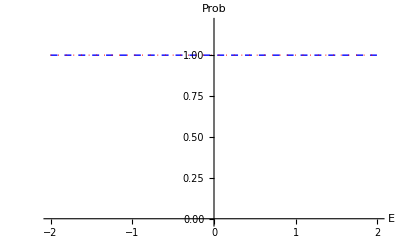

```mathematica
P=B11n+B12n +A11n+A12n +Te11n+Te12n+Th11n+Th12n;
P1=P/.{S-> 1/2,m1-> -1/2,J->4.5,kfa-> 0.85*π,Z-> 0.1,Δ-> 1,Ef-> 30};
P2=P/.{S-> 1/2,m1-> 0.49999,J-> 4.5,kfa-> 0.85*π,Z-> 0.1,Δ-> 1,Ef-> 30};

Plot[{P1,P2},{Ed,-2,2},PlotRange->{-0.02,1.2},PlotStyle->{{Blue,Dashed,Thick},{Red,Dotted,Thick},{Black,Dashed,Thick}},AxesLabel-> {"E","Prob"},PlotLegends->Placed[{""},{Right,Top}],LabelStyle->{FontSize->18}]
```

```mathematica
P1/.{Ed->2.5}
```

1.

```mathematica
Pdn=B11dn+B12dn +A11dn+A12dn +Te11dn+Te12dn+Th11dn+Th12dn;
P1dn=Pdn/.{S-> 1/2,m1-> -0.49999,J->4.5,kfa-> 0.85*π,Z-> 0.1,Δ-> 1,Ef-> 30};
P2dn=Pdn/.{S-> 1/2,m1-> 1/2,J-> 4.5,kfa-> 0.85*π,Z-> 0.1,Δ-> 1,Ef-> 30};

Plot[{P1dn,P2dn},{Ed,-2,2},PlotRange->{-0.02,1.2},PlotStyle->{{Blue,Dashed,Thick},{Red,Dotted,Thick},{Black,Dashed,Thick}},AxesLabel-> {"E","Prob"},PlotLegends->Placed[{""},{Right,Top}],LabelStyle->{FontSize->18}]
```

-Graphics-

```mathematica
P1dn/.{Ed-> 2.5}
```

1.

```mathematica
An=A//MatrixForm
```

(1 | 0 | 0 | 0 | -1 | 0 | -ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | -1 | 0 | -ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) | 0 | -1 | 0 | 0 | 0 | 0
-ⅈ J m1+√(1+Abs[Ed]/Ef) | -ⅈ J √((-m1+S) (1+m1+S)) | 0 | 0 | √(1+Abs[Ed]/Ef) | 0 | -ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) √(1+Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ J √((-m1+S) (1+m1+S)) | ⅈ J (1+m1)+√(1+Abs[Ed]/Ef) | 0 | 0 | 0 | √(1+Abs[Ed]/Ef) | 0 | -ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) √(1+Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ J (1+m1)-√(1-Abs[Ed]/Ef) | -ⅈ J √((-m1+S) (1+m1+S)) | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) √(1-Abs[Ed]/Ef) | 0 | -√(1-Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ J √((-m1+S) (1+m1+S)) | -ⅈ J m1-√(1-Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) √(1-Abs[Ed]/Ef) | 0 | -√(1-Abs[Ed]/Ef) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) | 0 | 0 | 0 | -ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) | 0 | 0 | 0 | -ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef))
0 | 0 | 0 | 0 | ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) (2 ⅈ Z-√(1+Abs[Ed]/Ef)) | 0 | 2 ⅈ Z+√(1+Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) √(1+Abs[Ed]/Ef) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) (2 ⅈ Z-√(1+Abs[Ed]/Ef)) | 0 | 2 ⅈ Z+√(1+Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) √(1+Abs[Ed]/Ef) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ Z-√(1-Abs[Ed]/Ef) | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) (2 ⅈ Z+√(1-Abs[Ed]/Ef)) | 0 | 0 | 0 | -ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) √(1-Abs[Ed]/Ef) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ Z-√(1-Abs[Ed]/Ef) | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) (2 ⅈ Z+√(1-Abs[Ed]/Ef)) | 0 | 0 | 0 | -ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) √(1-Abs[Ed]/Ef))

## Normalised Conductance

```mathematica
F=Sqrt[(S-m1)*(S+m1+1)];
F1=Sqrt[(S+m1)*(S-m1+1)];
```

```mathematica
A11n
A12n
```

0

0

```mathematica
A11dn
A12dn
```

0

0

```mathematica
B11n//Simplify
```

Abs[(Ef (Abs[Ed] (ⅈ J^2 S (1+S)-2 ⅈ ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) J (1+2 m1) Z-4 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+2 J m1 (2 ⅈ Z+√((Ef+Abs[Ed])/Ef)))+Ef (-4 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+J^2 S (1+S) (ⅈ-ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2+2 (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))-2 J (ⅇ^(4 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (1+m1) Z^2 √((Ef+Abs[Ed])/Ef)-ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (1+2 m1) Z (-ⅈ+Z √((Ef+Abs[Ed])/Ef))+m1 (-2 ⅈ Z-√((Ef+Abs[Ed])/Ef)+Z^2 √((Ef+Abs[Ed])/Ef))))))/(4 Abs[Ed]^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2

```mathematica
B12n//Simplify
```

4 Abs[(Ef^2 J √(-m1-m1^2+S+S^2) √((Ef+Abs[Ed])/Ef) (-ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+√((Ef+Abs[Ed])/Ef))^2)/(4 Abs[Ed]^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2

```mathematica
B11dn//Simplify
```

Abs[(Ef (ⅈ Abs[Ed] (J^2 S (1+S)+4 ⅈ ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+J (-4 m1 Z+2 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (-1+2 m1) Z+2 ⅈ m1 √((Ef+Abs[Ed])/Ef)))+Ef (-4 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+J^2 S (1+S) (ⅈ-ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2+2 (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J (ⅇ^(4 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (-1+m1) Z^2 √((Ef+Abs[Ed])/Ef)-ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (-1+2 m1) Z (-ⅈ+Z √((Ef+Abs[Ed])/Ef))+m1 (-2 ⅈ Z-√((Ef+Abs[Ed])/Ef)+Z^2 √((Ef+Abs[Ed])/Ef))))))/(4 Abs[Ed]^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2

```mathematica
B12dn//Simplify
```

4 Abs[(Ef J √(m1-m1^2+S+S^2) √((Ef+Abs[Ed])/Ef) (-Abs[Ed]+Ef (-1+(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2+2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))))/(4 Abs[Ed]^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2

```mathematica
Gcn =Simplify[(1-(B11n+B12n)+1-(B11dn+B12dn)),Element[Ed,Reals]];
```

```mathematica
Gcn
```

2-4 Abs[(Ef^2 J √(-m1-m1^2+S+S^2) √((Ef+Abs[Ed])/Ef) (-ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+√((Ef+Abs[Ed])/Ef))^2)/(4 Ed^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2-4 Abs[(Ef J √(m1-m1^2+S+S^2) √((Ef+Abs[Ed])/Ef) (-Abs[Ed]+Ef (-1+(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2+2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))))/(4 Ed^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2-Abs[(Ef (ⅈ Abs[Ed] (J^2 S (1+S)+4 ⅈ ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+J (-4 m1 Z+2 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (-1+2 m1) Z+2 ⅈ m1 √((Ef+Abs[Ed])/Ef)))+Ef (-4 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+J^2 S (1+S) (ⅈ-ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2+2 (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J (ⅇ^(4 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (-1+m1) Z^2 √((Ef+Abs[Ed])/Ef)-ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (-1+2 m1) Z (-ⅈ+Z √((Ef+Abs[Ed])/Ef))+m1 (-2 ⅈ Z-√((Ef+Abs[Ed])/Ef)+Z^2 √((Ef+Abs[Ed])/Ef))))))/(4 Ed^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2-Abs[(Ef (Abs[Ed] (ⅈ J^2 S (1+S)-2 ⅈ ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) J (1+2 m1) Z-4 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+2 J m1 (2 ⅈ Z+√((Ef+Abs[Ed])/Ef)))+Ef (-4 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+J^2 S (1+S) (ⅈ-ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2+2 (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))-2 J (ⅇ^(4 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (1+m1) Z^2 √((Ef+Abs[Ed])/Ef)-ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (1+2 m1) Z (-ⅈ+Z √((Ef+Abs[Ed])/Ef))+m1 (-2 ⅈ Z-√((Ef+Abs[Ed])/Ef)+Z^2 √((Ef+Abs[Ed])/Ef))))))/(4 Ed^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2

```mathematica
Gcn0=(Gcn/.{S-> 0.5,kfa-> 0.85*π,J->4.5,Ef-> 30,m1->0.49999})+(Gcn/.{S-> 0.5,kfa-> 0.85*π,J->4.5,Ef-> 30,m1->- 0.49999});
```

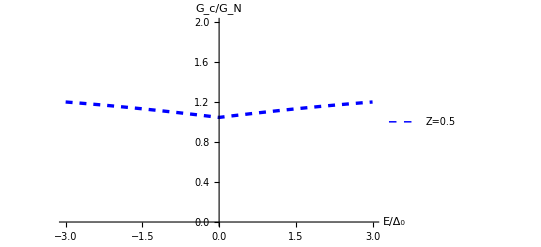

```mathematica
Plot[{Gcn0/2/.{Z-> 0.5}},{Ed,-3,3},PlotRange->{0.0,2},PlotStyle->{{Blue,Dashed,Thickness[0.006]},{Red,Dashed,Thickness[0.006]},{Black,Dashed,Thickness[0.006]}},AxesLabel->{"E/Δ_0","G_c/G_N"},AxesStyle->Black,PlotLegends->Placed[{"Z=0.5"},{Right,Top}],LabelStyle->{Bold,FontSize->17}]
```

## N-sf-N-I-S junction for YSR states

## Spin up incident electron

```mathematica
Clear["Global`*"]


(*S= 0.5;
kfa= 0.5*π;
m1= -0.5;
Δ= 1;
Ef= 30;
J= 1.2;
F= 1;*)

a1=1;
a2=0;
a3=0;
a4=0;
a5=-1;
a6=0;
a7=-Exp[I*kfa*ke1];
a8=0;
a9=0;
a10=0;
a11=0;
a12=0;
a13=0;
a14=0;
a15=0;
a16=0;
z1=-1;


b1=0;
b2=1;
b3=0;
b4=0;
b5=0;
b6=-1;
b7=0;
b8=-Exp[I*kfa*ke1];
b9=0;
b10=0;
b11=0;
b12=0;
b13=0;
b14=0;
b15=0;
b16=0;
z2=0;


c1=0;
c2=0;
c3=1;
c4=0;
c5=0;
c6=0;
c7=0;
c8=0;
c9=-Exp[-I*kfa*kh1];
c10=0;
c11=-1; 
c12=0; 
c13=0;
c14=0;
c15=0;
c16=0;
z3=0;


d1=0;
d2=0;
d3=0;
d4=1;
d5=0;
d6=0;
d7=0;
d8=0;
d9=0;
d10=-Exp[-I*kfa*kh1]; 
d11=0;
d12=-1;
d13=0;
d14=0;
d15=0;
d16=0;
z4=0;


e1=ke1-I*J*m1;
e2=-I*J*F;
e3=0;
e4=0;
e5=ke1;
e6=0;
e7=-ke1*Exp[I*kfa*ke1];
e8=0;
e9=0;
e10=0;
e11=0;
e12=0;
e13=0;
e14=0;
e15=0;
e16=0;
z5=ke1+I*J*m1;


f1=-I*J*F;
f2=ke1+I*J*(m1+1);
f3=0;
f4=0;
f5=0;
f6=ke1;
f7=0;
f8=-ke1*Exp[I*kfa*ke1];
f9=0;
f10=0;
f11=0;
f12=0;
f13=0;
f14=0;
f15=0;
f16=0;
z6=I*J*F;


g1=0;
g2=0;
g3=-kh1+I*J*(m1+1); (* - I*)
g4=-I*J*F;
g5=0;
g6=0;
g7=0;
g8=0;
g9=kh1*Exp[-I*kfa*kh1];
g10=0;
g11=-kh1;
g12=0;
g13=0;
g14=0;
g15=0;
g16=0;
z7=0;


h1=0;
h2=0;
h3=-I*J*F;
h4=-kh1-I*J*(m1);
h5=0;
h6=0;
h7=0;
h8=0;
h9=0;
h10=kh1*Exp[-I*kfa*kh1];
h11=0;
h12=-kh1;
h13=0;
h14=0;
h15=0;
h16=0;
z8=0;


i1=0;
i2=0;
i3=0;
i4=0;
i5=Exp[I*kfa*ke1]; 
i6=0;  
i7=1;
i8=0;
i9=0;
i10=0;
i11=0;
i12=0;
i13=-u*Exp[I*kfa*qp1]; 
i14=0;
i15=0;
i16=-v*Exp[-I*kfa*qm1]; 
z9=0;


j1=0;
j2=0;
j3=0;
j4=0;
j5=0;
j6=Exp[I*kfa*ke1];
j7=0;
j8=1;
j9=0;      
j10=0;
j11=0;
j12=0;
j13=0;
j14=-u*Exp[I*kfa*qp1];  
j15=v*Exp[-I*kfa*qm1];    
j16=0;
z10=0;


t1=0;
t2=0;
t3=0;
t4=0;
t5=0;
t6=0;
t7=0;
t8=0;
t9=1;
t10=0;
t11=Exp[-I*kfa*kh1]; 
t12=0;
t13=0;
t14=v*Exp[I*kfa*qp1];
t15=-u*Exp[-I*kfa*qm1];  
t16=0;      
z11=0;


l1=0;
l2=0;
l3=0;
l4=0;
l5=0;
l6=0;
l7=0;  
l8=0;
l9=0;
l10=1;
l11=0;
l12=Exp[-I*kfa*kh1];
l13=-v*Exp[I*kfa*qp1];
l14=0; 
l15=0;  
l16=-u*Exp[-I*kfa*qm1];
z12=0;


p1=0;
p2=0;
p3=0;
p4=0;
p5=-(ke1-I*2*Z)*Exp[I*kfa*ke1];                
p6=0; 
p7=(ke1+I*2*Z);
p8=0;
p9=0;
p10=0;
p11=0;
p12=0;
p13=u*qp1*Exp[I*kfa*qp1]; 
p14=0;
p15=0;
p16=-v*qm1*Exp[-I*kfa*qm1];
z13=0;


q1=0;
q2=0;
q3=0;
q4=0;
q5=0;
q6=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
q7=0;
q8=(ke1+I*2*Z);   
q9=0;
q10=0;
q11=0;
q12=0;
q13=0;
q14=u*qp1*Exp[I*kfa*qp1];
q15=v*qm1*Exp[-I*kfa*qm1];
q16=0;
z14=0;


r1=0;
r2=0;
r3=0;
r4=0;
r5=0;
r6=0;
r7=0;
r8=0;
r9=-(kh1-I*2*Z);
r10=0;   
r11=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
r12=0;
r13=0;
r14=-v*qp1*Exp[I*kfa*qp1];
r15=-u*qm1*Exp[-I*kfa*qm1];
r16=0; 
z15=0;


w1=0;
w2=0;
w3=0;
w4=0;
w5=0;
w6=0;
w7=0;   
w8=0;
w9=0;
w10=-(kh1-I*2*Z);
w11=0;
w12=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
w13=v*qp1*Exp[I*kfa*qp1];
w14=0;  
w15=0;  
w16=-u*qm1*Exp[-I*kfa*qm1];
z16=0;


A={{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16},{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,b16},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16},{d1,d2,d3,d4,d5,d6,d7,d8,d9,d10,d11,d12,d13,d14,d15,d16},{e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14,e15,e16},{f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16},{g1,g2,g3,g4,g5,g6,g7,g8,g9,g10,g11,g12,g13,g14,g15,g16},{h1,h2,h3,h4,h5,h6,h7,h8,h9,h10,h11,h12,h13,h14,h15,h16},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12,i13,i14,i15,i16 },{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14 ,j15 ,j16},{t1,t2,t3,t4,t5,t6,t7,t8,t9,t10,t11,t12,t13,t14 ,t15 ,t16},{l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,l11,l12,l13 ,l14,l15,l16 },{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13 ,p14,p15,p16 },{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14 ,q15 ,q16},{r1,r2,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,r13,r14 ,r15 ,r16},{w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,w11,w12,w13 ,w14,w15,w16 }}; 

B={z1,z2,z3,z4,z5,z6,z7,z8,z9,z10,z11,z12,z13,z14,z15,z16};
Sol=Refine[LinearSolve[A,B],Element[Ed,Reals]];
```

```mathematica
B11=Abs[Sol[[1]]]^2;
B12=Abs[Sol[[2]]]^2; 
A11=Re[kh1/ke1]Abs[Sol[[3]]]^2;                                   
A12=Re[kh1/ke1]Abs[Sol[[4]]]^2;
```

```mathematica
Te11=Re[qp1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sol[[13]]]^2;
Te12=Re[qp1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sol[[14]]]^2; 
Th11=Re[qm1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sol[[15]]]^2;                                   
Th12=Re[qm1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sol[[16]]]^2;
```

## Spin down incident electron

```mathematica
a1d=1; (* Subscript[r^du, ee]*)
a2d=0;
a3d=0;
a4d=0;
a5d=-1;
a6d=0;
a7d=-Exp[I*kfa*ke1];
a8d=0;
a9d=0;
a10d=0;
a11d=0;
a12d=0;
a13d=0;
a14d=0;
a15d=0;
a16d=0;
z1d=0;


b1d=0;
b2d=1; (* Subscript[r^dd, ee]*)
b3d=0;
b4d=0;
b5d=0;
b6d=-1;
b7d=0;
b8d=-Exp[I*kfa*ke1];
b9d=0;
b10d=0;
b11d=0;
b12d=0;
b13d=0;
b14d=0;
b15d=0;
b16d=0;
z2d=-1;


c1d=0;
c2d=0;
c3d=1;   (* Subscript[r^du, eh]*)
c4d=0;
c5d=0;
c6d=0;
c7d=0;
c8d=0;
c9d=-Exp[-I*kfa*kh1];
c10d=0;
c11d=-1; 
c12d=0; 
c13d=0;
c14d=0;
c15d=0;
c16d=0;
z3d=0;


d1d=0;
d2d=0;
d3d=0;
d4d=1;  (* Subscript[r^dd, eh]*)
d5d=0;
d6d=0;
d7d=0;
d8d=0;
d9d=0;
d10d=-Exp[-I*kfa*kh1]; 
d11d=0;
d12d=-1;
d13d=0;
d14d=0;
d15d=0;
d16d=0;
z4d=0;


e1d=ke1-I*J*(m1-1); (* Subscript[r^du, ee]*)
e2d=-I*J*F1 ;       (* Subscript[r^dd, ee]*)
e3d=0;
e4d=0;
e5d=ke1;
e6d=0;
e7d=-ke1*Exp[I*kfa*ke1];
e8d=0;
e9d=0;
e10d=0;
e11d=0;
e12d=0;
e13d=0;
e14d=0;
e15d=0;
e16d=0;
z5d=I*J*F1;


f1d=-I*J*F1;
f2d=ke1+I*J*m1;
f3d=0;
f4d=0;
f5d=0;
f6d=ke1;
f7d=0;
f8d=-ke1*Exp[I*kfa*ke1];
f9d=0;
f10d=0;
f11d=0;
f12d=0;
f13d=0;
f14d=0;
f15d=0;
f16d=0;
z6d=ke1-I*J*m1;


g1d=0;
g2d=0;
g3d=-kh1+I*J*(m1); 
g4d=-I*J*F1;
g5d=0;
g6d=0;
g7d=0;
g8d=0;
g9d=kh1*Exp[-I*kfa*kh1];
g10d=0;
g11d=-kh1;
g12d=0;
g13d=0;
g14d=0;
g15d=0;
g16d=0;
z7d=0;


h1d=0;
h2d=0;
h3d=-I*J*F1;
h4d=-kh1-I*J*(m1-1);
h5d=0;
h6d=0;
h7d=0;
h8d=0;
h9d=0;
h10d=kh1*Exp[-I*kfa*kh1];
h11d=0;
h12d=-kh1;
h13d=0;
h14d=0;
h15d=0;
h16d=0;
z8d=0;


i1d=0;
i2d=0;
i3d=0;
i4d=0;
i5d=Exp[I*kfa*ke1]; 
i6d=0;  
i7d=1;
i8d=0;
i9d=0;
i10d=0;
i11d=0;
i12d=0;
i13d=-u*Exp[I*kfa*qp1]; 
i14d=0;
i15d=0;
i16d=-v*Exp[-I*kfa*qm1]; 
z9d=0;


j1d=0;
j2d=0;
j3d=0;
j4d=0;
j5d=0;
j6d=Exp[I*kfa*ke1];
j7d=0;
j8d=1;
j9d=0;      
j10d=0;
j11d=0;
j12d=0;
j13d=0;
j14d=-u*Exp[I*kfa*qp1];  
j15d=v*Exp[-I*kfa*qm1];    
j16d=0;
z10d=0;


t1d=0;
t2d=0;
t3d=0;
t4d=0;
t5d=0;
t6d=0;
t7d=0;
t8d=0;
t9d=1;
t10d=0;
t11d=Exp[-I*kfa*kh1]; 
t12d=0;
t13d=0;
t14d=v*Exp[I*kfa*qp1];
t15d=-u*Exp[-I*kfa*qm1];  
t16d=0;      
z11d=0;


l1d=0;
l2d=0;
l3d=0;
l4d=0;
l5d=0;
l6d=0;
l7d=0;  
l8d=0;
l9d=0;
l10d=1;
l11d=0;
l12d=Exp[-I*kfa*kh1];
l13d=-v*Exp[I*kfa*qp1];
l14d=0; 
l15d=0;  
l16d=-u*Exp[-I*kfa*qm1];
z12d=0;


p1d=0;
p2d=0;
p3d=0;
p4d=0;
p5d=-(ke1-I*2*Z)*Exp[I*kfa*ke1];                
p6d=0; 
p7d=(ke1+I*2*Z);
p8d=0;
p9d=0;
p10d=0;
p11d=0;
p12d=0;
p13d=u*qp1*Exp[I*kfa*qp1]; 
p14d=0;
p15d=0;
p16d=-v*qm1*Exp[-I*kfa*qm1];
z13d=0;


q1d=0;
q2d=0;
q3d=0;
q4d=0;
q5d=0;
q6d=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
q7d=0;
q8d=(ke1+I*2*Z);   
q9d=0;
q10d=0;
q11d=0;
q12d=0;
q13d=0;
q14d=u*qp1*Exp[I*kfa*qp1];
q15d=v*qm1*Exp[-I*kfa*qm1];
q16d=0;
z14d=0;


r1d=0;
r2d=0;
r3d=0;
r4d=0;
r5d=0;
r6d=0;
r7d=0;
r8d=0;
r9d=-(kh1-I*2*Z);
r10d=0;   
r11d=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
r12d=0;
r13d=0;
r14d=-v*qp1*Exp[I*kfa*qp1];
r15d=-u*qm1*Exp[-I*kfa*qm1];
r16d=0; 
z15d=0;


w1d=0;
w2d=0;
w3d=0;
w4d=0;
w5d=0;
w6d=0;
w7d=0;   
w8d=0;
w9d=0;
w10d=-(kh1-I*2*Z);
w11d=0;
w12d=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
w13d=v*qp1*Exp[I*kfa*qp1];
w14d=0;  
w15d=0;  
w16d=-u*qm1*Exp[-I*kfa*qm1];
z16d=0;


Ad={{a1d,a2d,a3d,a4d,a5d,a6d,a7d,a8d,a9d,a10d,a11d,a12d,a13d,a14d,a15d,a16d},{b1d,b2d,b3d,b4d,b5d,b6d,b7d,b8d,b9d,b10d,b11d,b12d,b13d,b14d,b15d,b16d},{c1d,c2d,c3d,c4d,c5d,c6d,c7d,c8d,c9d,c10d,c11d,c12d,c13d,c14d,c15d,c16d},{d1d,d2d,d3d,d4d,d5d,d6d,d7d,d8d,d9d,d10d,d11d,d12d,d13d,d14d,d15d,d16d},{e1d,e2d,e3d,e4d,e5d,e6d,e7d,e8d,e9d,e10d,e11d,e12d,e13d,e14d,e15d,e16d},{f1d,f2d,f3d,f4d,f5d,f6d,f7d,f8d,f9d,f10d,f11d,f12d,f13d,f14d,f15d,f16d},{g1d,g2d,g3d,g4d,g5d,g6d,g7d,g8d,g9d,g10d,g11d,g12d,g13d,g14d,g15d,g16d},{h1d,h2d,h3d,h4d,h5d,h6d,h7d,h8d,h9d,h10d,h11d,h12d,h13d,h14d,h15d,h16d},{i1d,i2d,i3d,i4d,i5d,i6d,i7d,i8d,i9d,i10d,i11d,i12d,i13d,i14d,i15d,i16d},{j1d,j2d,j3d,j4d,j5d,j6d,j7d,j8d,j9d,j10d,j11d,j12d,j13d,j14d,j15d,j16d},{t1d,t2d,t3d,t4d,t5d,t6d,t7d,t8d,t9d,t10d,t11d,t12d,t13d,t14d,t15d,t16d},{l1d,l2d,l3d,l4d,l5d,l6d,l7d,l8d,l9d,l10d,l11d,l12d,l13d,l14d,l15d,l16d},{p1d,p2d,p3d,p4d,p5d,p6d,p7d,p8d,p9d,p10d,p11d,p12d,p13d,p14d,p15d,p16d},{q1d,q2d,q3d,q4d,q5d,q6d,q7d,q8d,q9d,q10d,q11d,q12d,q13d,q14d,q15d,q16d},{r1d,r2d,r3d,r4d,r5d,r6d,r7d,r8d,r9d,r10d,r11d,r12d,r13d,r14d,r15d,r16d},{w1d,w2d,w3d,w4d,w5d,w6d,w7d,w8d,w9d,w10d,w11d,w12d,w13d,w14d,w15d,w16d }}; 

Bd={z1d,z2d,z3d,z4d,z5d,z6d,z7d,z8d,z9d,z10d,z11d,z12d,z13d,z14d,z15d,z16d};
Sold=Refine[LinearSolve[Ad,Bd],Element[Ed,Reals]];
```

```mathematica
B11d=Abs[Sold[[2]]]^2;
B12d=Abs[Sold[[1]]]^2; 
A11d=Re[kh1/ke1]Abs[Sold[[4]]]^2;                                   
A12d=Re[kh1/ke1]Abs[Sold[[3]]]^2;
```

```mathematica
Te11d=Re[qp1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sold[[14]]]^2;
Te12d=Re[qp1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sold[[13]]]^2; 
Th11d=Re[qm1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sold[[16]]]^2;                                   
Th12d=Re[qm1/ke1](Abs[u]^2-Abs[v]^2)Abs[Sold[[15]]]^2;
```

## Probabilities

```mathematica
(*u=Piecewise[{{(1/2*(Abs[Ed]+I*(-Ed^2+Δ^2)^(1/2))/Δ)^(1/2),-Δ<Ed<Δ},{(1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),Ed≥ Δ},{(1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),Ed≤ -Δ}},1/2^(1/2)];

v = Piecewise[{{(1/2*(Abs[Ed]-I*(-Ed^2+Δ^2)^(1/2))/Δ)^(1/2),-Δ<Ed<Δ},{(1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),Ed≥ Δ},{(1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),Ed≤ -Δ}},1/2^(1/2)]; *)
```

```mathematica
(*u=(1/2*(Abs[Ed]+I*(-Ed^2+Δ^2)^(1/2))/Δ)^(1/2); v = (1/2*(Abs[Ed]-I*(-Ed^2+Δ^2)^(1/2))/Δ)^(1/2);*)
```

```mathematica
B1n=Abs[Sol[[1]]]^2/.{u-> 1,v-> 0,qp1-> ke1,qm1-> kh1};
B2n=Abs[Sol[[2]]]^2/.{u-> 1,v-> 0,qp1-> ke1,qm1-> kh1};
A1n=Re[kh1/ke1]Abs[Sol[[3]]]^2/.{u-> 1,v-> 0,qp1-> ke1,qm1-> kh1};
A2n=Re[kh1/ke1]Abs[Sol[[4]]]^2/.{u-> 1,v-> 0,qp1-> ke1,qm1-> kh1};
```

```mathematica
u
```

```mathematica
u=Piecewise[{{(1/2*(1+((Ed^2-Δ^2)^(1/2))/Abs[Ed]))^(1/2),Abs[Ed]>Δ},{(1/2*(1+(I(-Ed^2+Δ^2)^(1/2))/Abs[Ed]))^(1/2),Abs[Ed]<Δ}}]; 
v=Piecewise[{{(1/2*(1-((Ed^2-Δ^2)^(1/2))/Abs[Ed]))^(1/2),Abs[Ed]>Δ},{(1/2*(1-(I(-Ed^2+Δ^2)^(1/2))/Abs[Ed]))^(1/2),Abs[Ed]<Δ}}];
```

```mathematica
F=Sqrt[(S-m1)*(S+m1+1)];
F1=Sqrt[(S+m1)*(S-m1+1)];
```

```mathematica
ke1=√(1+Abs[Ed]/Ef);
kh1=√(1-Abs[Ed]/Ef);
qp1=Piecewise[{{√(1+((Ed^2-Δ^2)^(1/2))/Ef),Abs[Ed]>Δ},{√(1+(I(-Ed^2+Δ^2)^(1/2))/Ef),Abs[Ed]<Δ}}];
qm1=Piecewise[{{√(1-((Ed^2-Δ^2)^(1/2))/Ef),Abs[Ed]>Δ},{√(1-(I(-Ed^2+Δ^2)^(1/2))/Ef),Abs[Ed]<Δ}}];
```

```mathematica
B1n=B11/.{Δ-> 0};
B2n=B12/.{Δ-> 0};
A1n=A11/.{Δ-> 0};
A2n=A12/.{Δ-> 0};
```

```mathematica
B1n/.{S-> 0.5,m1-> -1/2,J->4.5,kfa-> 0.85*π,Z-> 1,Ed-> 0.2}
```

```mathematica
B11/.{S-> 1/2,m1-> -1/2,J->4.5,kfa-> 0.85*π,Z-> 0.1,Ed-> 0.2}
```

Abs[-1+1/1-((1) (-8 5 ((2 3 (1-1)-1) (1)-1)+1))/(-(1) (1)+((2 3 (1-1)-1) (1)-1) 1)]^2
 |  |  |  |

```mathematica
P=B11+B12 +A11+A12 +Te11+Te12+Th11+Th12;
P1=P/.{S-> 1/2,m1-> -1/2,J->4.5,kfa-> 0.85*π,Z-> 0.1,Δ-> 1,Ef-> 30};
P2=P/.{S-> 1/2,m1-> 0.49999,J-> 4.5,kfa-> 0.85*π,Z-> 0.1,Δ-> 1,Ef-> 30};

Plot[{P1,P2},{Ed,-2,2},PlotRange->{-0.02,1.2},PlotStyle->{{Blue,Dashed,Thick},{Red,Dotted,Thick},{Black,Dashed,Thick}},AxesLabel-> {"E","Prob"},PlotLegends->Placed[{""},{Right,Top}],LabelStyle->{FontSize->18}]
```

-Graphics-

```mathematica
P1/.{Ed->2.5}
```

1.

```mathematica
Pd=B11d+B12d +A11d+A12d +Te11d+Te12d+Th11d+Th12d;
P1d=Pd/.{S-> 1/2,m1-> -0.49999,J->4.5,kfa-> 0.85*π,Z-> 0.1,Δ-> 1,Ef-> 30};
P2d=Pd/.{S-> 1/2,m1-> 1/2,J-> 4.5,kfa-> 0.85*π,Z-> 0.1,Δ-> 1,Ef-> 30};

Plot[{P1d,P2d},{Ed,-2,2},PlotRange->{-0.02,1.2},PlotStyle->{{Blue,Dashed,Thick},{Red,Dotted,Thick},{Black,Dashed,Thick}},AxesLabel-> {"E","Prob"},PlotLegends->Placed[{""},{Right,Top}],LabelStyle->{FontSize->18}]
```

-Graphics-

```mathematica
P1d/.{Ed-> 2.5}
```

1.

```mathematica
A/.{u-> (1/2*(Abs[Ed]+I*(-Ed^2+Δ^2)^(1/2))/Δ)^(1/2),v-> (1/2*(Abs[Ed]-I*(-Ed^2+Δ^2)^(1/2))/Δ)^(1/2)}//MatrixForm
```

(1 | 0 | 0 | 0 | -1 | 0 | -ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | -1 | 0 | -ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) | 0 | -1 | 0 | 0 | 0 | 0
-ⅈ J m1+√(1+Abs[Ed]/Ef) | -ⅈ J √((-m1+S) (1+m1+S)) | 0 | 0 | √(1+Abs[Ed]/Ef) | 0 | -ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) √(1+Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ J √((-m1+S) (1+m1+S)) | ⅈ J (1+m1)+√(1+Abs[Ed]/Ef) | 0 | 0 | 0 | √(1+Abs[Ed]/Ef) | 0 | -ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) √(1+Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ J (1+m1)-√(1-Abs[Ed]/Ef) | -ⅈ J √((-m1+S) (1+m1+S)) | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) √(1-Abs[Ed]/Ef) | 0 | -√(1-Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ J √((-m1+S) (1+m1+S)) | ⅈ J m1-√(1-Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) √(1-Abs[Ed]/Ef) | 0 | -√(1-Abs[Ed]/Ef) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -(ⅇ^(ⅈ kfa (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ))/(√2) | 0 | 0 | -(ⅇ^(-ⅈ kfa (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((-ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ))/(√2)
0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -(ⅇ^(ⅈ kfa (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ))/(√2) | (ⅇ^(-ⅈ kfa (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((-ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ))/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) | 0 | 0 | (ⅇ^(ⅈ kfa (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((-ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ))/(√2) | -(ⅇ^(-ⅈ kfa (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ))/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) | -(ⅇ^(ⅈ kfa (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((-ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ))/(√2) | 0 | 0 | -(ⅇ^(-ⅈ kfa (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ))/(√2)
0 | 0 | 0 | 0 | ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) (2 ⅈ Z-√(1+Abs[Ed]/Ef)) | 0 | 2 ⅈ Z+√(1+Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0 | (ⅇ^(ⅈ kfa (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ) (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}]))/(√2) | 0 | 0 | -(ⅇ^(-ⅈ kfa (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((-ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ) (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}]))/(√2)
0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ kfa √(1+Abs[Ed]/Ef)) (2 ⅈ Z-√(1+Abs[Ed]/Ef)) | 0 | 2 ⅈ Z+√(1+Abs[Ed]/Ef) | 0 | 0 | 0 | 0 | 0 | (ⅇ^(ⅈ kfa (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ) (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}]))/(√2) | (ⅇ^(-ⅈ kfa (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((-ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ) (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}]))/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ Z-√(1-Abs[Ed]/Ef) | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) (2 ⅈ Z+√(1-Abs[Ed]/Ef)) | 0 | 0 | -(ⅇ^(ⅈ kfa (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((-ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ) (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}]))/(√2) | -(ⅇ^(-ⅈ kfa (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ) (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}]))/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ Z-√(1-Abs[Ed]/Ef) | 0 | ⅇ^(-ⅈ kfa √(1-Abs[Ed]/Ef)) (2 ⅈ Z+√(1-Abs[Ed]/Ef)) | (ⅇ^(ⅈ kfa (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((-ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ) (Piecewise[{{√(1+(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1+(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}]))/(√2) | 0 | 0 | -(ⅇ^(-ⅈ kfa (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}])) √((ⅈ √(-Ed^2+Δ^2)+Abs[Ed])/Δ) (Piecewise[{{√(1-(√(Ed^2-Δ^2))/Ef), Abs[Ed]>Δ}, {√(1-(ⅈ √(-Ed^2+Δ^2))/Ef), Abs[Ed]<Δ}, {0, True}}]))/(√2))

## Conductance

```mathematica
u=(1/2*(1+((Ed^2-Δ^2)^(1/2))/Abs[Ed]))^(1/2); (*(1/2*(1+(I(-Ed^2+Δ^2)^(1/2))/Abs[Ed]))^(1/2); *)
v=(1/2*(1-((Ed^2-Δ^2)^(1/2))/Abs[Ed]))^(1/2) ;(*(1/2*(1-((Ed^2-Δ^2)^(1/2))/Abs[Ed]))^(1/2)*)
ke1=√(1+Abs[Ed]/Ef);
kh1=√(1-Abs[Ed]/Ef);
qp1=√(1+((Ed^2-Δ^2)^(1/2))/Ef);(*Piecewise[{{√(1+((Ed^2-Δ^2)^(1/2))/Ef),Abs[Ed]>Δ},{√(1+(I(-Ed^2+Δ^2)^(1/2))/Ef),Abs[Ed]<Δ}}];*)
qm1=√(1-((Ed^2-Δ^2)^(1/2))/Ef); (*Piecewise[{{√(1-((Ed^2-Δ^2)^(1/2))/Ef),Abs[Ed]>Δ},{√(1-(I(-Ed^2+Δ^2)^(1/2))/Ef),Abs[Ed]<Δ}}];*)
```

```mathematica
F=Sqrt[(S-m1)*(S+m1+1)];
F1=Sqrt[(S+m1)*(S-m1+1)];
```

```mathematica
Gcn=2-4 Abs[(Ef^2 J √(-m1-m1^2+S+S^2) √((Ef+Abs[Ed])/Ef) (-ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+√((Ef+Abs[Ed])/Ef))^2)/(4 Ed^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2-4 Abs[(Ef J √(m1-m1^2+S+S^2) √((Ef+Abs[Ed])/Ef) (-Abs[Ed]+Ef (-1+(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2+2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))))/(4 Ed^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2-Abs[(Ef (ⅈ Abs[Ed] (J^2 S (1+S)+4 ⅈ ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+J (-4 m1 Z+2 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (-1+2 m1) Z+2 ⅈ m1 √((Ef+Abs[Ed])/Ef)))+Ef (-4 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+J^2 S (1+S) (ⅈ-ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2+2 (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J (ⅇ^(4 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (-1+m1) Z^2 √((Ef+Abs[Ed])/Ef)-ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (-1+2 m1) Z (-ⅈ+Z √((Ef+Abs[Ed])/Ef))+m1 (-2 ⅈ Z-√((Ef+Abs[Ed])/Ef)+Z^2 √((Ef+Abs[Ed])/Ef))))))/(4 Ed^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2-Abs[(Ef (Abs[Ed] (ⅈ J^2 S (1+S)-2 ⅈ ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) J (1+2 m1) Z-4 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+2 J m1 (2 ⅈ Z+√((Ef+Abs[Ed])/Ef)))+Ef (-4 ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) Z (ⅈ Z+√((Ef+Abs[Ed])/Ef))+J^2 S (1+S) (ⅈ-ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2+2 (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))-2 J (ⅇ^(4 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (1+m1) Z^2 √((Ef+Abs[Ed])/Ef)-ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)) (1+2 m1) Z (-ⅈ+Z √((Ef+Abs[Ed])/Ef))+m1 (-2 ⅈ Z-√((Ef+Abs[Ed])/Ef)+Z^2 √((Ef+Abs[Ed])/Ef))))))/(4 Ed^2+Ef Abs[Ed] (8+J^2 S (1+S)+2 (-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) J Z-4 Z^2+2 ⅈ J √((Ef+Abs[Ed])/Ef)+8 ⅈ Z √((Ef+Abs[Ed])/Ef))+Ef^2 (4-4 Z^2+8 ⅈ Z √((Ef+Abs[Ed])/Ef)+J^2 S (1+S) (1-(-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef)))^2 Z^2-2 ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z √((Ef+Abs[Ed])/Ef))+2 J ((-2+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z+ⅈ √((Ef+Abs[Ed])/Ef)+ⅈ (-1+ⅇ^(2 ⅈ kfa √((Ef+Abs[Ed])/Ef))) Z^2 √((Ef+Abs[Ed])/Ef))))]^2;
```

```mathematica
Gcn0=Gcn/.{S-> 0.5,kfa-> 0.843*π,J->4.5,Ef-> 30};
```

```mathematica
Gc =(1-(B11+B12)+(A11+A12)+1-(B11d+B12d)+(A11d+A12d))/.{Δ-> 1};
```

```mathematica
G1=(Gc/2)/.{S-> 0.5,kfa-> 0.843*π,J->4.5,Ef-> 30};
```

```mathematica
G1avg=(G1/.{m1->-0.49999})+(G1/.{m1->0.49999});
```

```mathematica
G1avgn=(G1/Gcn0/.{m1->-0.49999})+(G1/Gcn0/.{m1->0.49999});
```

```mathematica
G1avg/.{Z-> 0.776,Ed-> 0.00001}
```

1.86982

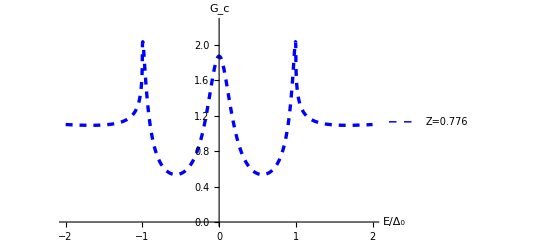

```mathematica
Plot[{G1avg/.{Z-> 0.776}},{Ed,-2,2},PlotRange->{0.0,2.25},PlotStyle->{{Blue,Dashed,Thickness[0.006]},{Red,Dashed,Thickness[0.006]},{Black,Dashed,Thickness[0.006]}},AxesLabel->{"E/Δ_0","G_c"},AxesStyle->Black,PlotLegends->Placed[{"Z=0.776"},{Right,Top}],LabelStyle->{Bold,FontSize->17}]
```

```mathematica
G1avgn/.{Z-> 0.776,Ed-> 0.0001}
```

2.12559

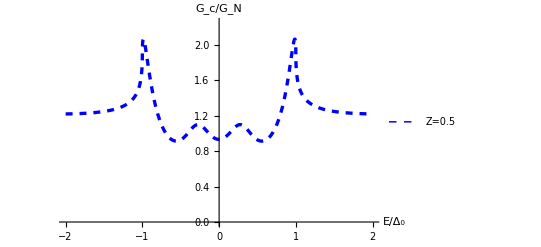

```mathematica
Plot[{G1avg/.{Z-> 0.5}},{Ed,-2,2},PlotRange->{0.0,2.25},PlotStyle->{{Blue,Dashed,Thickness[0.006]},{Red,Dashed,Thickness[0.006]},{Black,Dashed,Thickness[0.006]}},AxesLabel->{"E/Δ_0","G_c/G_N"},AxesStyle->Black,PlotLegends->Placed[{"Z=0.5"},{Right,Top}],LabelStyle->{Bold,FontSize->17}]
```

```mathematica
Plot[{G1avgn/.{Z-> 0.776}},{Ed,-2,2},PlotRange->{0.0,2.25},PlotStyle->{{Blue,Dashed,Thickness[0.006]},{Red,Dashed,Thickness[0.006]},{Black,Dashed,Thickness[0.006]}},AxesLabel->{"E/Δ_0","G_c/G_N"},AxesStyle->Black,PlotLegends->Placed[{"Z=0.776"},{Right,Top}],LabelStyle->{Bold,FontSize->17}]
```

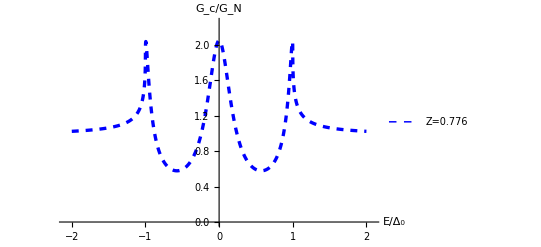

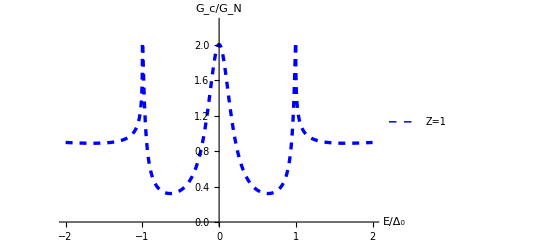

```mathematica
Plot[{G1avg/.{Z-> 1}},{Ed,-2,2},PlotRange->{0.0,2.25},PlotStyle->{{Blue,Dashed,Thickness[0.006]},{Red,Dashed,Thickness[0.006]},{Black,Dashed,Thickness[0.006]}},AxesLabel->{"E/Δ_0","G_c/G_N"},AxesStyle->Black,PlotLegends->Placed[{"Z=1"},{Right,Top}],LabelStyle->{Bold,FontSize->17}]
```